# Lab M3: Physical Pendulum

## Introduction

The main purpose of this lab is to understand the concept of angular motion. Angular motion can be described by τ=Iα (torque=Moment of inertia * angular acceleration). This is slightly different than a simple pedulum because the mass is distributed throughout the lenght of the meter stick. A physical pendulum is a rigid object which swings freely about some pivot point.

## Data

Introduction to Part 1: Check of the theory

For the first part of the lab, the measurement of the period would take place for 8 different pivot points on a physical pendulum (the meter stick). The main goal for this procedure is to confirm that the data collected matched the line generated by the theory of the physical pendulum.

Introduction to Part 2: Measurement of g

The main goal for this part of the lab is to use the data taken in the previous part and use it to make an approximation of the acceleration to gravity (in other words, calculated the gravitational constant). This can be provided by the slope of the graph of T^2vs r^2, which in theory would have a slope of 4 π^2/g.

Part 1 Data:

```mathematica
n= 8;(*Number of measurements taken*)
T={1.6312,1.6137,1.5704,1.5632,1.5251,1.5242,1.5361,1.5644}; (*The period for each of the 8 measurements (s)*)
x1= {49,47,41,40,31,30,21,20}; (*Distance from the pivot point to the center of meter stick (cm)*)
δT= 0.0001; (*Uncertainity in period (s)*)
δx1= 0.05; (*Uncertainity in distance (cm)*)
r=x1-(0.16/2) ;
(*Distance from the pivot point to the center of the meter stick minus the radius of the pivot rod, 0.16cm is the given diameter of the pivot rod (cm)*)
δr=δx1; (*Uncertainity in r will be the same as δx as they both are calculated on the same meter stick used (cm)*)
table= Thread[{ T, x1, r}]; Grid[Prepend[table,{"Period (s)", "Distance from center (cm)","x-(0.16/2) (cm)"}], Frame-> All]
```

Period (s) | Distance from center (cm) | x-(0.16/2) (cm)
1.6312 | 49 | 48.92
1.6137 | 47 | 46.92
1.5704 | 41 | 40.92
1.5632 | 40 | 39.92
1.5251 | 31 | 30.92
1.5242 | 30 | 29.92
1.5361 | 21 | 20.92
1.5644 | 20 | 19.92

## Data Analysis

Part 1: Check of the Theory

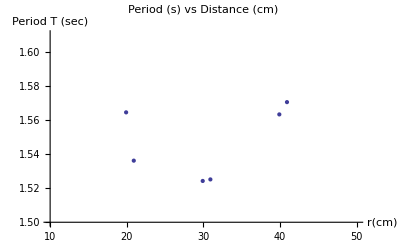

```mathematica
Tvsd= Thread[{r,T}]; ListPlot[{Tvsd}, PlotLabel->"Period (s) vs Distance (cm)", AxesLabel-> {"r(cm)", "Period T (sec)"}, PlotRange -> {{10,50},{1.5,1.61}}]
```

As seen above this graph doesn’t have a linear line nor a constant slope. Hence, another graph would be plotted with g/(4 π^2)T^2 r vs. r^2. In theory the slope should be constant the line should be linear.

```mathematica
g=9.796; (*The gravitational constant given to us in the lab manual (m/s^2)*)
T2=g/(4 π^2)T^2(r/100);
r2=(r/100)^2;
Ptable= Thread[{r2,T2}];
Grid[Prepend[Ptable,{"Distance squared (m^2)","g/(4 SuperscriptBox[π, 2])T^2(r/100)"}], Frame-> All]
```

Distance squared (m^2) | g/(4 SuperscriptBox[π, 2])T^2(r/100)
0.239317 | 0.322991
0.220149 | 0.303174
0.167445 | 0.250406
0.159361 | 0.242052
0.0956046 | 0.178454
0.0895206 | 0.172478
0.0437646 | 0.122487
0.0396806 | 0.120969

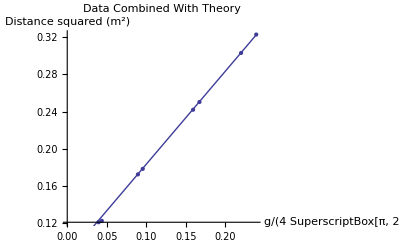

0.0803071+1.0149 x

```mathematica
data={{0.23931664000000002,0.3229906226120775},{0.22014864,0.3031744798849471},{0.16744464,0.2504062924014407},{0.15936064,0.24205199424257676},{0.09560464000000002,0.1784535398421752},{0.08952064000000001,0.17247833197997495},{0.04376464000000001,0.12248691549667745},{0.03968064,0.12096897154748264}};
graph2=ListPlot[data];
f[x_]=x+(1/12);
graph3=Plot[f[x],{x,0,0.4892^2}];
Show[graph2,graph3,PlotLabel->"Data Combined With Theory", AxesLabel->{"g/(4 SuperscriptBox[π, 2])T^2r","Distance squared (m^2)"}]
Fit[data,{1,x},x]
```

As shown above, the line infact is linear with a constant slope. The error of the slope can be determined through the y intercept shown above, whcih happens to be ±0.015.

Part 2: Measurement of g

```mathematica
T3=T^2(r/100) (*y Data points used to plot another graph in linfit.nb file*)
r3=(r/100)^2(*x data points used to plot another graph in linfit.nb fil*)
```

{1.30167,1.22181,1.00915,0.975483,0.719178,0.695097,0.493629,0.487512}

{0.239317,0.220149,0.167445,0.159361,0.0956046,0.0895206,0.0437646,0.0396806}

The data as been interpreted as x=r3 and y=T3, where both were plugged into the linfit.nb file of mathematica and the results have been attached.

```mathematica
m=4.09009; (*The slope of the graph acquired by linefit.nb*)
δm=0.0237837; (*Uncertainity in the slope of the graph acquired by linefit.nb*)
gslope=4 π^2/m
δgslope=gslope*δm/m(*Calculated value multiplied by the fractional error*)
```

9.65221

0.0561272

In standard format, the value of g would be 9.65 ± 0.06 m/s^2. This isn’t extremely accurate as the literature value happens to be 9.796 m/s^2.

```mathematica
b=0.323642; (*This is the y-intercept of the best fit line*)
δb=0.00356722;(*This is the uncertainity of the y-intercept of the best fit line*)
gintercept=4 π^2/(12b)(*L^2 equalizes to 1 due to the fact that we were using a meter stick*)
δgintercept=gintercept*δb/b
```

10.1651

0.112041

In standard format, the value of the y intercept is 10.17 ± 0.11 m/s^2.

## Conclusion

Part 1: Check of the Theory

In this particular part of the lab, we compared the measured and theoretical values of the slopes and intercepts of our graphs. We used different pivot points that were more than 15 cm away from the center of the meter stick and used a photogate to measure the time it took the meter stick to complete 10 periods. Then the measured values for the distance and the period gave us a parabolic graph and showed that the values with a similar distance from the center yielded a similar period. The second graph compared the equation g/(4 π^2)T^2 r vs. r^2. This graph gave a linear relationship, thus we compared it to the theory line. The calculated values and the theoretical values were extremely close to each other, allowing me to say that there was less than 5% of error in the performance of this part fo the lab. The slight difference between the theoretical values and the calculated values could be due to human error by the person who drilled the holes in the meter stick. If these points weren’t ideal, then the data could be misguided giving slight inaccurate periods. Leading to slight discrepencies. If there was a longer distance measured than it would yield a smaller period. Another limitation could be a systematic error from the photogate. In order to improve this lab in the future, we could apply smaller amplitudes each time or this experiment could be done in a vacuum to reduce air resistance.

Part 2: Measurement of g

In the last part fo this lab, we compared the measured value of g with the known value of g. We used the data and plotted a graph of T^2 r vs. r^2. The slope of this graph is predicted to be 4 π^2/(12g)L.Hence, the linfit.nb file was used to calculate the slope, y-intercept and the uncertainties of the slope and y intercept. First, we compared the graph T^2 r vs. r^2 and yielded a linear comparison between the two. This could be explained by the fact that as distance gets bigger, period increases as well. The slope was calculated to be 9.65 ± 0.06 m/s^2 and the y-intercept was calculated to be 10.17 ± 0.11 m/s^2. The have a slight discrepency. The discrepency can be explained by human error with applying the amplitude. We didn’t wait for the ruler stick to complete an initial period before starting the photogate which means that wobbling of the meter stick is not ruled out. Waiting for the wobbling to stop and move smoothly is essential to any experiment to have consistent data with as low uncertainity as possible. Other than that, the value of g calculated was close to the literature value of 9.796 m/s^2. To improve our data, this lab should be redone in a vacuum to reduce air resistance as well as wait for several periods before taking any data for the wobbling to stop, allowing less uncertainty and more accurate data results.